```mathematica
Directory[]
```

/Users/kuzubatomohiko/Documents/修士1年/多変量解析/多変量解析,5:8

```mathematica
SetDirectory["/Users/kuzubatomohiko/Documents/修士1年/多変量解析/多変量解析,5:8"]
```

/Users/kuzubatomohiko/Documents/修士1年/多変量解析/多変量解析,5:8

```mathematica
名古屋の降水量データ=Import["precipitation.csv"];
名古屋の降水量データ//MatrixForm;
```

```mathematica
名古屋の降水量データ1=Drop[名古屋の降水量データ,1];
名古屋の降水量データ1//MatrixForm;
```

```mathematica
名古屋の降水量データ2=Transpose[名古屋の降水量データ1];
名古屋の降水量データ2//MatrixForm
```

(1891 | 1892 | 1893 | 1894 | 1895 | 1896 | 1897 | 1898 | 1899 | 1900 | 1901 | 1902 | 1903 | 1904 | 1905 | 1906 | 1907 | 1908 | 1909 | 1910 | 1911 | 1912 | 1913 | 1914 | 1915 | 1916 | 1917 | 1918 | 1919 | 1920 | 1921 | 1922 | 1923 | 1924 | 1925 | 1926 | 1927 | 1928 | 1929 | 1930 | 1931 | 1932 | 1933 | 1934 | 1935 | 1936 | 1937 | 1938 | 1939 | 1940 | 1941 | 1942 | 1943 | 1944 | 1945 | 1946 | 1947 | 1948 | 1949 | 1950 | 1951 | 1952 | 1953 | 1954 | 1955 | 1956 | 1957 | 1958 | 1959 | 1960 | 1961 | 1962 | 1963 | 1964 | 1965 | 1966 | 1967 | 1968 | 1969 | 1970 | 1971 | 1972 | 1973 | 1974 | 1975 | 1976 | 1977 | 1978 | 1979 | 1980 | 1981 | 1982 | 1983 | 1984 | 1985 | 1986 | 1987 | 1988 | 1989 | 1990 | 1991 | 1992 | 1993 | 1994 | 1995 | 1996 | 1997 | 1998 | 1999 | 2000 | 2001 | 2002 | 2003 | 2004 | 2005 | 2006 | 2007 | 2008 | 2009 | 2010 | 2011 | 2012 | 2013 | 2014 | 2015 | 2016
1519.9 | 1653.3 | 1292.4 | 1446.8 | 1736.3 | 2323.6 | 1908.8 | 1703.1 | 1871.6 | 1559.5 | 1439.9 | 1881 | 2128.1 | 2088.8 | 2115.7 | 1554 | 1921.7 | 1745.8 | 1676.8 | 1761.5 | 1683.3 | 1357.5 | 1297.3 | 1337.2 | 1791.5 | 1825.3 | 1714.5 | 1791.5 | 1729.3 | 1778.9 | 2024.7 | 1441.3 | 1809.9 | 1261.4 | 1813.5 | 1102.1 | 1176.9 | 1800.1 | 1518.9 | 1426.3 | 1601.8 | 1677.7 | 1318.9 | 1228.7 | 1910.7 | 1514.4 | 1504.2 | 1779.1 | 1311.5 | 1127 | 1801.1 | 1334.4 | 1168.4 | 1248.9 | 2075.4 | 1525 | 1087.8 | 1406.8 | 1630.5 | 1776.2 | 1600.2 | 1769.1 | 1715.2 | 1718.3 | 1425.7 | 1665.6 | 1726.2 | 1441.9 | 1904.6 | 1399 | 1517.1 | 1503.6 | 1278.3 | 1256.1 | 1556 | 1655.6 | 1602 | 1414.5 | 1386.5 | 1633.5 | 1877.5 | 1879.5 | 1166 | 1791.5 | 1607.5 | 2028.5 | 1367 | 1103.5 | 1526.5 | 1727 | 1525 | 1600.5 | 1627.5 | 1105 | 1589.5 | 1349.5 | 1234.5 | 1589.5 | 1643.5 | 1903.5 | 1990 | 1413.5 | 1726.5 | 1061 | 1393 | 1157 | 1610 | 1979.5 | 1628.5 | 1735.5 | 1415 | 1082.5 | 1905 | 1947.5 | 900.5 | 1611.5 | 1269.5 | 1579.5 | 1755.5 | 1730 | 1785.5 | 1567.5 | 1463.5 | 1505.5 | 1803 | 1686)

```mathematica
名古屋の降水量データ2[[2]]//MatrixForm
```

(1519.9
1653.3
1292.4
1446.8
1736.3
2323.6
1908.8
1703.1
1871.6
1559.5
1439.9
1881
2128.1
2088.8
2115.7
1554
1921.7
1745.8
1676.8
1761.5
1683.3
1357.5
1297.3
1337.2
1791.5
1825.3
1714.5
1791.5
1729.3
1778.9
2024.7
1441.3
1809.9
1261.4
1813.5
1102.1
1176.9
1800.1
1518.9
1426.3
1601.8
1677.7
1318.9
1228.7
1910.7
1514.4
1504.2
1779.1
1311.5
1127
1801.1
1334.4
1168.4
1248.9
2075.4
1525
1087.8
1406.8
1630.5
1776.2
1600.2
1769.1
1715.2
1718.3
1425.7
1665.6
1726.2
1441.9
1904.6
1399
1517.1
1503.6
1278.3
1256.1
1556
1655.6
1602
1414.5
1386.5
1633.5
1877.5
1879.5
1166
1791.5
1607.5
2028.5
1367
1103.5
1526.5
1727
1525
1600.5
1627.5
1105
1589.5
1349.5
1234.5
1589.5
1643.5
1903.5
1990
1413.5
1726.5
1061
1393
1157
1610
1979.5
1628.5
1735.5
1415
1082.5
1905
1947.5
900.5
1611.5
1269.5
1579.5
1755.5
1730
1785.5
1567.5
1463.5
1505.5
1803
1686)

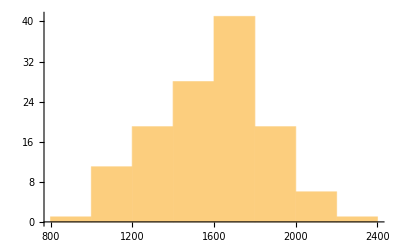

```mathematica
p1=Histogram[名古屋の降水量データ2[[2]]]
```

```mathematica
y=Drop[名古屋の降水量データ2,1]//Transpose;
```

```mathematica
σ=StandardDeviation[y];
```

```mathematica
μ=Mean[名古屋の降水量データ2[[2]]];
```

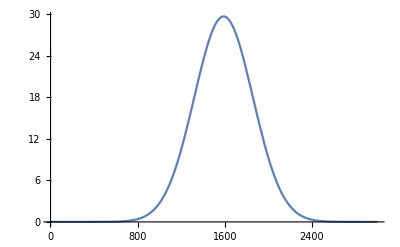

```mathematica
p2=Plot[20000/(√(2π (σ)^2))Exp[-(y-μ)^2/(2 σ^2)],{y,1,3000}]
```

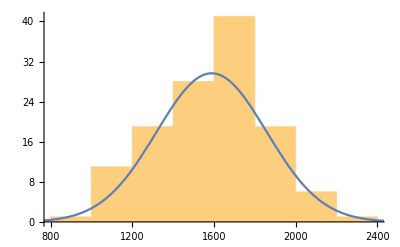

```mathematica
Show[p1,p2]
```

```mathematica
(1/10)*(1/5)*(3/10)*(2/5)*(1/2)*(3/5)*(7/10)*(4/5)*(9/10)
```

```mathematica
N[567/1562500]
```

0.00036288